# Numerical Methods Project

Fahim Hussain

```mathematica
(** I used R to code my work and transferred my work from there to here **)
```

```mathematica
Quarterbacks
<-c("Mathhew Stafford","Carson Palmer","Drew Brees","Kirk Cousins","Joe Flacco","Aaron Rodgers","Russel Wilson","Ben Roethlisberger","Eli Manning","Philip Rivers")
Years<-c("2012","2013","2014","2015","2016","2017")

Strafford_TD<-c(20,29,22,32,24,21)
Strafford_Int<-c(17,19,12,13,10,6)
Strafford_Yds<-c(212,168,254,251,216,198)
Strafford_Games<-c(16,16,16,16,16,11)
Strafford_Cmp<-c(435,371,363,398,388,247)
Strafford_Att<-c(727,634,602,592,594,395)

Palmer_Td<-c(22,24,11,35,26,9)
Palmer_Int<-c(14,22,3,11,14,7)
Palmer_Yds<-c(4018,4274,1626,4671,4233,1978)
Palmer_Games<-c(15,16,6,16,15,7)
Palmer_Cmp<-c(345,362,141,342,364,164)
Palmer_Att<-c(565,572,224,537,597,267)

Brees_TD<-c(43,39,33,32,37,16)
Brees_Int<-c(19,12,17,11,15,5)
Brees_Yds<-c(5177,5162,4952,4870,5208,3029)
Brees_Games<-c(16,16,16,15,16,11)
Brees_Cmp<-c(422,446,456,428,471,266)
Brees_Att<-c(670,650,659,627,673,373)

Cousins_Td<-c(4,4,10,29,25,19)
Cousins_Int<-c(3,7,9,11,12,6)
Cousins_Yds<-c(466,854,1710,4166,4917,3038)
Cousins_Games<-c(1,3,5,16,16,11)
Cousins_Cmp<-c(33,81,126,379,406,249)
Cousins_Att<-c(48,155,204,543,606,376)

Flacco_Td<-c(22,19,27,14,20,9)
Flacco_Int<-c(10,22,12,12,15,11)
Flacco_Yds<-c(3817,3912,3986,2791,4317,1875)
Flacco_Games<-c(5,5,5,5,5,5)
Flacco_Cmp<-c(317,362,344,266,436,229)
Flacco_Att<-c(531,614,554,413,672,351)

Rodgers_Td<-c(39,17,38,31,40,13)
Rodgers_Int<-c(8,6,5,8,7,3)
Rodgers_Yds<-c(4295,2536,4381,3821,4428,1385)
Rodgers_Games<-c(16,9,16,16,16,6)
Rodgers_Cmp<-c(371,193,341,347,401,128)
Rodgers_Att<-c(552,290,520,572,610,193)

Roethlisberger_Td<-c(26,28,32,21,29,20)
Roethlisberger_Int<-c(8,14,9,16,13,12)
Roethlisberger_Yds<-c(3265,4261,4952,3938,3819,2948)
Roethlisberger_Games<-c(13,16,16,11,14,11)
Roethlisberger_Cmp<-c(284,375,408,319,328,250)
Roethlisberger_Att<-c(449,584,608,469,509,397)

Wilson_Td<-c(26,26,20,34,21,23)
Wilson_Int<-c(10,9,7,8,11,8)
Wilson_Yds<-c(3118,3357,3475,4024,4219,3029)
Wilson_Games<-c(16,16,16,16,16,11)
Wilson_Cmp<-c(252,257,285,329,353,256)
Wilson_Att<-c(393,407,452,483,546,411)

Manning_Td<-c(26,18,30,36,26,14)
Manning_Int<-c(15,27,14,14,16,7)
Manning_Yds<-c(3948,3818,4410,4432,4027,2411)
Manning_Games<-c(10,10,10,10,10,10)
Manning_Cmp<-c(321,317,379,387,377,247)
Manning_Att<-c(536,551,601,618,598,395)

Rivers_Td<-c(26,32,31,29,33,20)
Rivers_Int<-c(15,11,18,13,21,7)
Rivers_Yds<-c(3606,4478,4286,4792,4386,2948)
Rivers_Games<-c(16,16,16,16,16,11)
Rivers_Cmp<-c(338,378,379,437,349,241)
Rivers_Att<-c(527,544,570,661,578,388)

Strafford_Salary<-c(27000000)
Palmer_Salary<-c(24350000)
Brees_Salary<-c(24250000)
Cousins_Salary<-c(23943600)
Flacco_Salary<-c(22133333)
Rodgers_Salary<-c(22000000)
Wilson_Salary<-c(21900000)
Roethlisberger_Salary<-c(21850000)
Manning_Salary<-c(21000000)
Rivers_Salary<-c(20812500)

Salaries<-rbind(Strafford_Salary,Palmer_Salary,Brees_Salary,Cousins_Salary,Flacco_Salary,Rodgers_Salary,Wilson_Salary,Roethlisberger_Salary,Manning_Salary,Rivers_Salary)
rm(Strafford_Salary,Palmer_Salary,Brees_Salary,Cousins_Salary,Flacco_Salary,Rodgers_Salary,Wilson_Salary,Roethlisberger_Salary,Manning_Salary,Rivers_Salary)

Touchdowns<-rbind(Strafford_TD,Palmer_Td,Brees_TD,Cousins_Td,Flacco_Td,Rodgers_Td,Wilson_Td,Roethlisberger_Td,Manning_Td,Rivers_Td)

rm(Strafford_TD,Palmer_Td,Brees_TD,Cousins_Td,Flacco_Td,Rodgers_Td,Roethlisberger_Td,Wilson_Td,Manning_Td,Rivers_Td)

Interceptions<-rbind(Strafford_Int,Palmer_Int,Brees_Int,Cousins_Int,Flacco_Int,Rodgers_Int,Wilson_Int,Roethlisberger_Int,Manning_Int,Rivers_Int)

rm(Strafford_Int,Palmer_Int,Brees_Int,Cousins_Int,Flacco_Int,Rodgers_Int,Roethlisberger_Int,Wilson_Int,Manning_Int,Rivers_Int)

Yards<-rbind(Strafford_Yds,Palmer_Yds,Brees_Yds,Cousins_Yds,Flacco_Yds,Rodgers_Yds,Wilson_Yds,Roethlisberger_Yds,Manning_Yds,Rivers_Yds)

rm(Strafford_Yds,Palmer_Yds,Brees_Yds,Cousins_Yds,Flacco_Yds,Rodgers_Yds,Roethlisberger_Yds,Wilson_Yds,Manning_Yds,Rivers_Yds)

Games<-rbind(Strafford_Games,Palmer_Games,Brees_Games,Cousins_Games,Flacco_Games,Rodgers_Games,Wilson_Games,Roethlisberger_Games,Manning_Games,Rivers_Games)

rm(Strafford_Games,Palmer_Games,Brees_Games,Cousins_Games,Flacco_Games,Rodgers_Games,Wilson_Games,Roethlisberger_Games,Manning_Games,Rivers_Games)

Completion<-rbind(Strafford_Cmp,Palmer_Cmp,Brees_Cmp,Cousins_Cmp,Flacco_Cmp,Rodgers_Cmp,Wilson_Cmp,Roethlisberger_Cmp,Manning_Cmp,Rivers_Cmp)

rm(Strafford_Cmp,Palmer_Cmp,Brees_Cmp,Cousins_Cmp,Flacco_Cmp,Rodgers_Cmp,Roethlisberger_Cmp,Wilson_Cmp,Manning_Cmp,Rivers_Cmp)

Attempts<-rbind(Strafford_Att,Palmer_Att,Brees_Att,Cousins_Att,Flacco_Att,Rodgers_Att,Wilson_Att,Roethlisberger_Att,Manning_Att,Rivers_Att)

rm(Strafford_Att,Palmer_Att,Brees_Att,Cousins_Att,Flacco_Att,Rodgers_Att,Roethlisberger_Att,Wilson_Att,Manning_Att,Rivers_Att)

rownames(Interceptions)<-Quarterbacks
rownames(Touchdowns)<-Quarterbacks
rownames(Salaries)<-Quarterbacks
rownames(Completion)<-Quarterbacks
rownames(Games)<-Quarterbacks
rownames(Yards)<-Quarterbacks
rownames(Attempts)<-Quarterbacks
colnames(Interceptions)<-Years
colnames(Touchdowns)<-Years
colnames(Completion)<-Years
colnames(Games)<-Years
colnames(Yards)<-Years
colnames(Attempts)<-Years
colnames(Salaries)<-"2017-2018"
```

```mathematica
plot<-function(data=Touchdowns,label,qb=1:10){Data<-data[qb,,drop=F] 
matplot(t(Data),type="l",pch=5:15,col=c(1:10),main="Football Statistics",xlab="Years",ylab=label,xaxt="n",font.lab=2) legend("topright",inset=c(-0.4,0),legend=Quarterbacks[qb],col=c(1:10),pch=5:15) par(mar=c(5.1,4.1,4.1,10.1),xpd=TRUE) axis(side=1,font=2,at=1:ncol(data),labels=Years) axis(side=2,font=2)}

plot(Yards/Completion,"Yards per Completed Passes")
```

## Are they worth what they’re worth?

```mathematica
2017-2018
Mathhew Stafford 27000000
Carson Palmer 24350000
Drew Brees 24250000
Kirk Cousins 23943600
Joe Flacco 22133333
Aaron Rodgers 22000000
Russel Wilson 21900000
Ben Roethlisberger 21850000
Eli Manning 21000000
Philip Rivers 20812500
```

```mathematica
(** Possibly, there are too many variables to take in to determine whether they are worth what they are truly worth **)
```

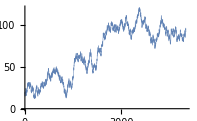
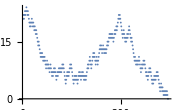
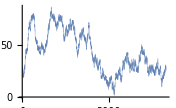
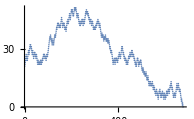
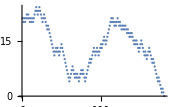
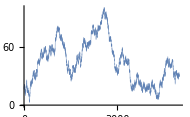
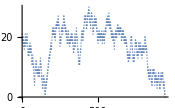
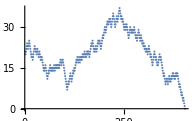
```mathematica
Gambler Ruin
p=0.505;
q=0.495;
n=20;
i=1;
m=5000;
money ={};
sequence=RandomChoice[{p,q}->{1,0},m];
While[n>0,
If[i≤m,
If[sequence[[i]]==1,
n=n+1;i++;AppendTo[money,n],
n=n-1 ; i++;AppendTo[money,n]
],
Break[]]];
Bets={};
For[i=1,i≤Length[money],i++,
AppendTo[Bets,i]]
ListPlot[Thread[{Bets,money}]]
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
(** These graphs are when p=0.5 and q=0.5, the point of these graphs is to show that even with equal probability, as you continue to play more and more games you're likely to go broke. I.E The house always wins **) 
(** There's a corollary that says that if p <= q, then it is certain that you will go broke if you continue playing an infinite amount of time **)
```